### Std of growth in the T, log (RCA) plane

```mathematica
(*SetDirectory[NotebookDirectory[]];
data = Import["XlogRCAplane_counts.csv"]//Rest;
Show[ListContourPlot[data,AspectRatio->Full,ColorFunction->(Lighter[Blue,#]&),ColorFunctionScaling->{1,0},Contours->20,ContourStyle->None,ClippingStyle->Automatic, LabelStyle->Directive[Bold, 18],FrameLabel->{"T","log(RCA)"},PlotRange->{{3.5,10},{-4,2}}],
ContourPlot[{logRCA+T == {3,6,9}},{T,3.5,10},{logRCA,-4,2},FrameLabel->{"T = Tc + Tp - Tw","log(RCA)"},AspectRatio->Full,ContourStyle->Dashed,LabelStyle->Large]]
Export["TlRCAplane.png",%];*)
```

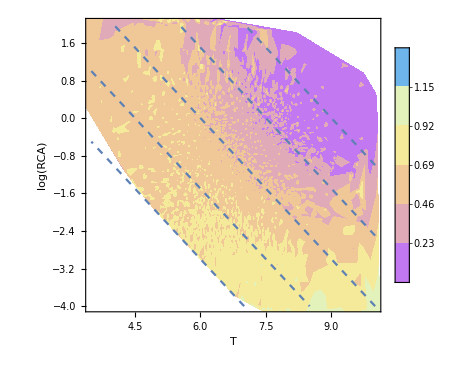

```mathematica
data = Import["stdGrowth.csv"]//Rest;
Show[ListContourPlot[data,AspectRatio->Full,Contours->5,ContourStyle->None,ClippingStyle->Automatic,ColorFunction->"Pastel", LabelStyle->Directive[Bold, 18],FrameLabel->{"T","log(RCA)","σ of log(x_cp) growth"},PlotRange->{{3.5,10},{-4,2}},PlotLegends->Automatic],
ContourPlot[{logRCA+T == {3,4.5,6,7.5,9}},{T,3.5,10},{logRCA,-4,2},FrameLabel->{"T = Tc + Tp - Tw","log(RCA)"},AspectRatio->Full,ContourStyle->Dashed,LabelStyle->Large]]
Export["stdGrowth_TlRCAplane.png",%];
```

### Early drafts on log (RCA)

```mathematica
Tw =  1*^14;
```

```mathematica
Tw=.
```

```mathematica
RCA[x_, Tc_, Tp_, Tw_:Tw]:= (x Tw)/(Tc Tp)
```

```mathematica
Log[10,RCA[(10^g)x, Tc+(10^g )x-x, Tp+(10^g )x-x,Tw+(10^g )x-x]]/Log[10,RCA[x, Tc, Tp]]
```

Log[(10^g x (Tw-x+10^g x))/((Tc-x+10^g x) (Tp-x+10^g x))]/Log[(Tw x)/(Tc Tp)]

```mathematica
Series[Log[(x (1+ϵ) (Tw+ϵ))/((Tc+ϵ) (Tp+ϵ))]/Log[(Tw x)/(Tc Tp)],{ϵ,0,4}];
```

```mathematica
Log10[(10^g)x(Tw+(10^g )x-x)/(Tc+(10^g )x-x)/(Tp+(10^g )x-x)]
```

Log[(10^g x (Tw-x+10^g x))/((Tc-x+10^g x) (Tp-x+10^g x))]/Log[10]

```mathematica
Series[Log10[(10^g)x(Tw+(10^g )x-x)/(Tc+(10^g )x-x)/(Tp+(10^g )x-x)],{g, 0, 2}]//Simplify
```

Log[(Tw x)/(Tc Tp)]/Log[10]+(1-x/Tc-x/Tp+x/Tw) g+(x (-Tc Tp^2 Tw^2+Tp^2 Tw^2 x+Tc^2 (Tp-Tw) (Tp (Tw-x)-Tw x)) Log[10] g^2)/(2 Tc^2 Tp^2 Tw^2)+O[g]^3

```mathematica
Log10[x Tw/Tc/Tp]
```

Log[(Tw x)/(Tc Tp)]/Log[10]

```mathematica
Log10[Series[RCA[(10^g)x, Tc+(10^g )x-x, Tp+(10^g )x-x,Tw+(10^g )x-x],{g, 0, 2}]/RCA[x, Tc, Tp]]//Simplify
```

(1-x/Tc-x/Tp+x/Tw) g+(x (-Tc Tp^2 Tw^2+Tp^2 Tw^2 x+Tc^2 (Tp-Tw) (Tp (Tw-x)-Tw x)) Log[10] g^2)/(2 Tc^2 Tp^2 Tw^2)+O[g]^3

```mathematica
pl=Normal@ContourPlot[1 - 1/x - 1/y,{x,1*^8,1*^12},{y,1*^7,1*^11},PlotPoints->100];
```

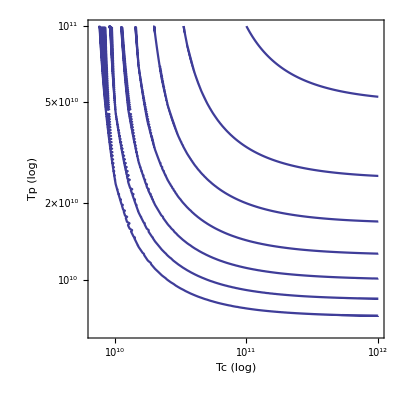

```mathematica
ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1],FrameLabel->{"Tc (log)", "Tp (log)"}]
```

```mathematica
1/
```

```mathematica
Solve[{1/Tw == 1/Tc + 1/Tp},Tp]
```

{{Tp→(Tc Tw)/(Tc-Tw)}}

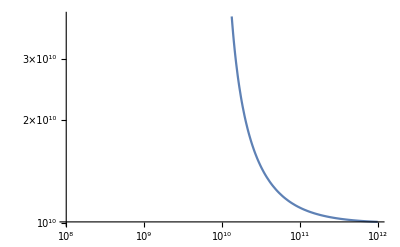

```mathematica
Tw =1*^10;
LogLogPlot[(Tc Tw)/(Tc-Tw), {Tc,1*^8,1*^12}]
```

```mathematica
Plot[Table[10^(-(1-1/10^x - 1/10^y )*0.01),{y,7,11}],{x, 8,12},PlotRange->{{8,12},{.96,1}}];
```

```mathematica
Plot[Table[10^(-(1-1/10^x - 1/10^y )*0.01),{x, 8,12}],{y,7,11},PlotRange->{{7,11},{.96,1}}];
```

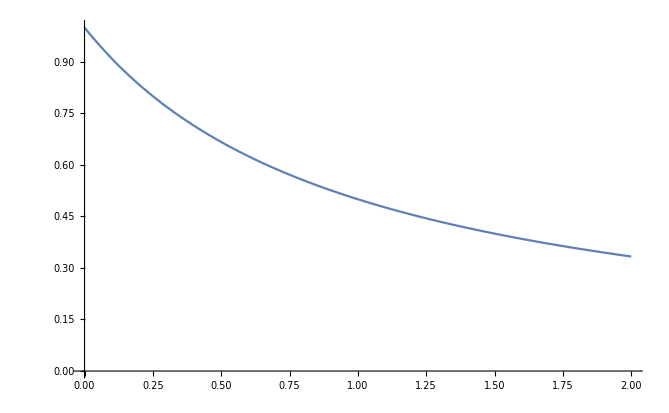

```mathematica
Plot[{1/(1+ϵ)},{ϵ,0,2},PlotRange->{{0,2},{0,1}}]
```

```mathematica
lRCA[lx_, lTc_, lTp_, lTw_:lTw]:= lx +lTw-lTc -lTp
```

```mathematica
lRCA[lx+lk, Tc+ϵ, Tp+ϵ,Tw+ϵ]/lRCA[x, Tc, Tp]
```

```mathematica
Series[RCA[x(1+ϵ), Tc+ϵ, Tp+ϵ,Tw+ϵ]/RCA[x, Tc, Tp],{ϵ, 0, 2}]
```

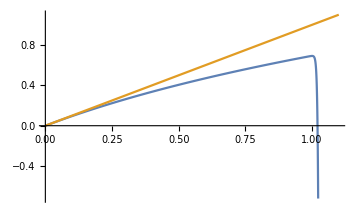

```mathematica
Plot[{Sum[-(-1)^n ϵ^n/n,{n,1,300}],ϵ},{ϵ,0,1.1}]
```

### Fit with Laplace

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data =Table[ Import["probGrowth_fit_data"<>ToString[i]<>".csv"]//Rest,{i,0,40,1}];
data = Select[#,#[[2]]>-9&]&/@data;
```

```mathematica
xv = Import["xVals.csv"]//Rest;
xcVals = xv[[All,1]];
xcmin = xv[[All,2]];
xcmax = xv[[All,3]];
```

#### Do fits

```mathematica
f[x_,μ_]:=Piecewise[{{k- Abs[(x-μ)/b1],x<μ},{k- Abs[(x-μ)/b2],μ≤x}}]
(*nlm = Table[NonlinearModelFit[data[[i]],{f[g,μ],b1<2,b1>0,b2<2, b2>0,μ<0.4, μ>-0.3},{{k,0},{μ,0}, {b1, 0.5},{b2, 0.5}},g],{i,1,41,1}]//Quiet;*)
(*nlm = Table[NonlinearModelFit[data[[i]],{k-(g-μ)^2/(2 σ^2),σ>0},{{k,0}, {μ, 0},{σ, 0.1}},g],{i,1,41,1}]//Quiet;*)(*nlm = Table[NonlinearModelFit[data[[i]],{k- Abs[(g-μ)/b],b<2,b>0,μ<0.7, μ>-0.3},{{k,0},{μ,0}, {b, 0.5}},g],{i,1,41,1}]//Quiet;*)
nlm = Table[NonlinearModelFit[data[[i]],{k- Abs[(g-0.0)/b],b<2,b>0},{{k,0},{b, 0.5}},g],{i,1,41,1}]//Quiet;
(*plots =Show[ Table[{ListPlot[data[[i]],PlotRange->{{-1,1},{-5,-2}}],Plot[nlm[[i]][g],{g,-.8,2}]},{i,11,31,5}],ImageSize->300]//Quiet;*)
norm = -Log[Table[NIntegrate[E^(nlm[[i]][g]),{g, -Infinity,Infinity}],{i,1,41,1}]];
```

#### Plot in linear scale

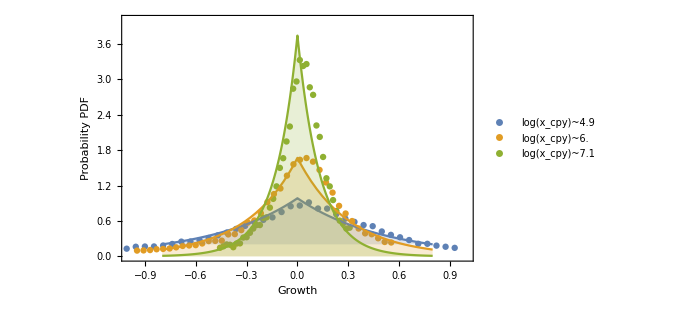

```mathematica
data=Select[#,#[[2]]>-9&]&/@Table[ Import["probGrowth_fit_data"<>ToString[i]<>".csv"]//Rest,{i,0,40,1}];
Do[data[[i,All,2]] = norm[[i]]+data[[i,All,2]] ,{i,1,41,1}]
Do[data[[i,All,2]] = E^(data[[i,All,2]]) ,{i,1,41,1}]
j = Table[i,{i,11,31,10}];
Show[ListPlot[Table[data[[j[[i]]]],{i,Length[j]}],PlotLegends->Table["log(x_cpy)~"<>ToString[Round[xcVals[[j[[i]]]],.1]],{i,Length[j]}],PlotRange->{{-1,1},{0,4}}],
Show[Table[Plot[E^(norm[[j[[i]]]]+nlm[[j[[i]]]][g]),{g,-.8,.8},PlotStyle->ColorData[97,"ColorList"][[i]],Filling->Bottom],{i,Length[j]}]],Frame->True,FrameLabel->{"Growth","Probability PDF"},LabelStyle->16,ImageSize->500]
Export["Exp_dists_fit.png",%];
```

#### Plot in log scale

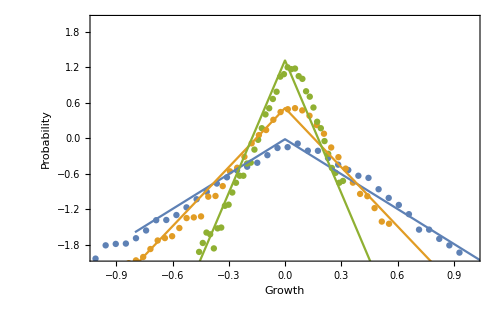

```mathematica
data=Select[#,#[[2]]>-9&]&/@Table[ Import["probGrowth_fit_data"<>ToString[i]<>".csv"]//Rest,{i,0,40,1}];
Do[data[[i,All,2]] = norm[[i]]+data[[i,All,2]] ,{i,1,41,1}]
j = Table[i,{i,11,31,10}];
Show[ListPlot[Table[data[[j[[i]]]],{i,Length[j]}],PlotRange->{{-1,1},{-2,2}}],
Show[Table[Plot[norm[[j[[i]]]]+nlm[[j[[i]]]][g],{g,-.8,2},PlotStyle->ColorData[97,"ColorList"][[i]]],{i,Length[j]}]],Frame->True,FrameLabel->{"Growth","Probability"},LabelStyle->20,ImageSize->500]
Export["Laplace_fit.png",%];
```

#### Fit dependence of std

```mathematica
(*nlmParams = Table[NonlinearModelFit[data[[i]],{k- Abs[(g-μ)/b],b<3,b>0,μ<0.7, μ>-0.3},{{k,0},{μ,0}, {b, 0.5}},g]["BestFitParameters"],{i,1,41,1}]//Quiet;*)
nlmParams = Table[NonlinearModelFit[data[[i]],{k- Abs[(g-0.00)/b],b<3,b>0},{{k,0},{b, 0.5}},g]["BestFitParameters"],{i,1,41,1}]//Quiet;
```

```mathematica
(*line1 = Fit[({xcVals, b1/.#&/@nlmParams}//Transpose//Rest)[[4;;]], {1,x},x]//Quiet*)
(*line2 = Fit[({xcVals, b2/.#&/@nlmParams}//Transpose//Rest)[[4;;]], {1,x},x]//Quiet*)
(*Show[ListPlot[{({xcVals, b1/.#&/@nlmParams}//Transpose//Rest)[[4;;]],({xcVals, b2/.#&/@nlmParams}//Transpose//Rest)[[4;;]]},Joined->True,PlotMarkers->Automatic], Plot[{line1, line2}, {x, 4, 10}]]//Quiet*)
dat = ({xcVals,Log10[ b/.#&/@nlmParams]}//Transpose);
bfit [x_]= Fit[dat[[4;;-4]],{x,1},x]
Show[ListPlot[dat],Plot[bfit[x],{x,xcVals[[4]],xcVals[[-4]]}],Frame->True,FrameLabel->{"Log(x_cpy)","Log(σ)"},LabelStyle->20,ImageSize->500]
Export["slopes_std_fit.png",%];
```

1.02317-0.264931 x

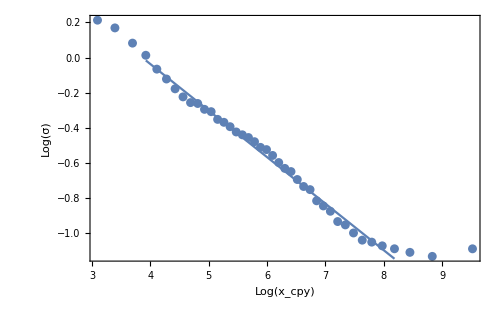

```mathematica
10^(1.0231746385237601)-0.26493052955725493 x
```

#### Mean and check for normalization...

```mathematica
dat = ({xcVals,μ/.#&/@nlmParams}//Transpose)[[6;;-6]];
μfit [x_]= Fit[dat,{1},x]
Show[ListPlot[dat],Plot[μfit[x],{x,3.5,8}],Frame->True,FrameLabel->{"Log(x_cpy)","Log(σ)"},LabelStyle->15]
```

1. μ

-Graphics-

```mathematica
k- Abs[(g-0.00)/b]/.NonlinearModelFit[data[[21]],{k- Abs[(g-0.00)/b],b<10,b>0},{{k,0},{b, 0.5}},g]["BestFitParameters"]
```

0.511953-3.33709 Abs[0.+g]

0.299662

0.273121

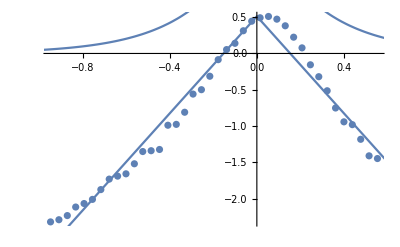

```mathematica
i=21;
10^(dat[[i]])[[2]]
x0=xcVals[[i]];
10^(bfit[x0])
Show[ListPlot[data[[i]]],Plot[(Exp[-Abs[g-0.00]/10^(bfit[x0])])/(2 10^(bfit[x0])),{g,-2,2}],Plot[0.5119528145684413-3.337092681173777 Abs[0.+g],{g,-2,2}]]
```

### Growth probabilities

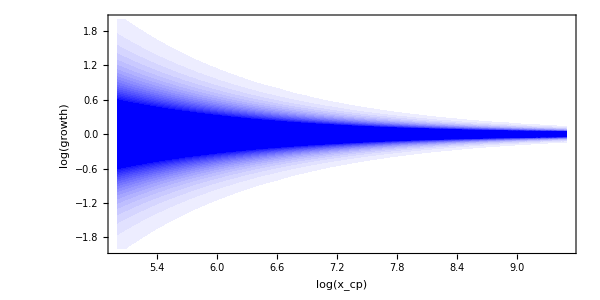

```mathematica
ContourPlot[ (Exp[-Abs[g-0.00]/10^(bfit[x])]),{x,5,9.5},{g,-2,2},AspectRatio->1/2,ImageSize->600,ColorFunction->(Lighter[Blue,#]&),ColorFunctionScaling->{1,0},Contours->20,ContourStyle->None,ClippingStyle->Automatic, LabelStyle->Directive[Bold, 18],FrameLabel->{"log(x_cp)","log(growth)"}]
Export["growth_dist_model.png",%];
```

```mathematica
numPgx = Import["Pgx.csv"]//Rest;
```

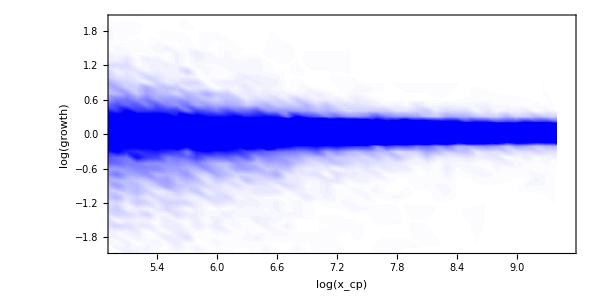

```mathematica
ListContourPlot[numPgx,AspectRatio->1/2,ImageSize->600,ContourStyle->None,ColorFunction->(Lighter[Blue,#]&),ColorFunctionScaling->{1,0},Contours->50,ClippingStyle->Automatic,PlotRange->{{5,9.5},{-2,2}}, LabelStyle->Directive[Bold, 18],FrameLabel->{"log(x_cp)","log(growth)"}]
Export["growth_dist_data.png",%];
```

### Drafts on Normal - Laplace extrapolation

```mathematica
β = 1;
Integrate[Exp[-Abs[(x/β)]^(3/2)],{x, -Infinity, Infinity}]
```

2 Gamma[5/3]

{0.00737777,0.0295983,0.0668175,0.119314,0.186434,0.262536,0.361419,0.472264,0.59735,0.737956,0.89335,1.06672,1.23254,1.45246,1.66461,1.88459,2.13125,2.42342,2.64835,2.96127}

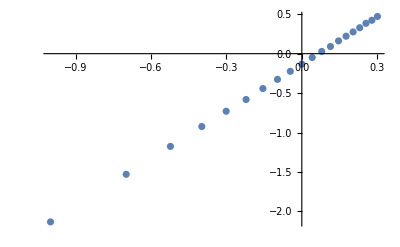

-0.131544+1.99902 x

```mathematica
v =Table[β = i;
d =ProbabilityDistribution[(1/( β 2 Gamma[5/3]))Exp[-Abs[(x/β)]^(3/2)],{x,-Infinity,Infinity}];
data=RandomVariate[d,10^5];
Variance[data],{i,0.1,2, 0.1}]
bVar = Log10[{Table[i,{i,0.1,2, 0.1}],v}//Transpose];
ListPlot[bVar]
Fit[bVar, {1,x},x]
```

```mathematica
10^(-0.1310355729491823)
10^(-0.13154353880261566)
```

0.739545

0.73868

```mathematica
1/Sqrt[2]//N
```

0.707107

```mathematica
20480/12//N
```

1706.67

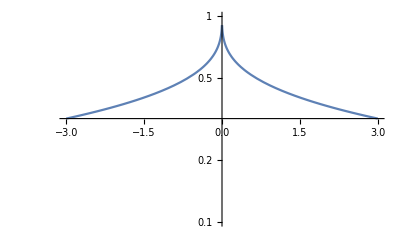

```mathematica
LogPlot[Exp[-Abs[(x/β)]^(1/3)],{x,-3,3}, PlotRange->{All, {0.1,1}}]
```

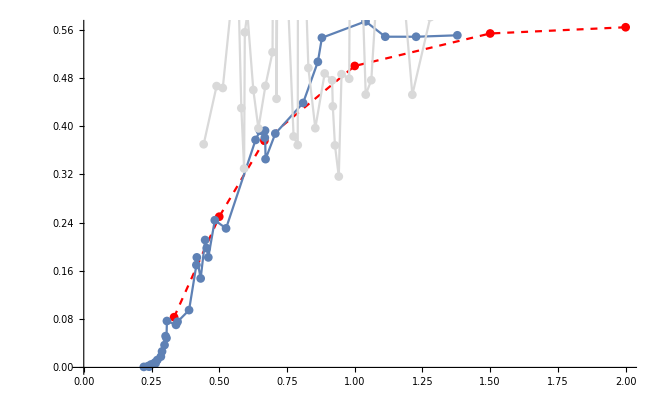

```mathematica
Show[ListPlot[{{1/3,1/12},{1/2,1/4},{2/3,2/(3Sqrt[Pi])},{1,1/2},{3/2,1/(2 Gamma[5/3])},{2, 1/Sqrt[Pi]}},Joined->True,PlotStyle->Directive[Dashed,Red],PlotMarkers->Automatic],
ListPlot[SortBy[{t1/.#&/@nlmParams[[4;;]],b1/.#&/@nlmParams[[4;;]]*Exp[1.9+k/.#&/@nlmParams[[4;;]]]}//Transpose,First]//Most,Joined->True,PlotMarkers->Automatic],
ListPlot[SortBy[{t2/.#&/@nlmParams[[4;;]],b2/.#&/@nlmParams[[4;;]]*Exp[1.9+k/.#&/@nlmParams[[4;;]]]}//Transpose,First]//Most,Joined->True,PlotMarkers->Automatic,PlotStyle->LightGray]]
```

### Drafts of contour plots

1.01351

```mathematica
bfit[[2,1]]
```

-0.267341

```mathematica
Exp[bfit]
```

ⅇ^(1.01351-0.267341 x)

```mathematica
c1 = -0.05522717466746096;
c2 = 4.663714686950169;
x0 = 2.2647998090548245;
k1 = 0.7359;
k2 = -0.0305;
Xw = 13.1;
Xp = 9.3;
```

```mathematica
Table[Xc+Xp-Xw,{Xc,5,9.5,0.5}]
```

{1.2,1.7,2.2,2.7,3.2,3.7,4.2,4.7,5.2,5.7}

```mathematica
Xc = 10;
Xp = 9.3;
Xw=13.1;
v = Table[{logRCA,Xc} =xy[[i]];t = logRCA+Xc+Xp-Xw;{logRCA,Xc,NIntegrate[Exp[-Abs[g-0.03]/(c1 +c2 Exp[-x/x0])]* Exp[-(x-t)^2/(2(k1 t +k2)^2)]/((c1 +c2 Exp[-x/x0])*Sqrt[2Pi](k1 t +k2)),{x,t-3,t+3},{g,-logRCA,Infinity}]/norm},{i,1,Length[xy]}]//Quiet;
ListContourPlot[v]
```

```mathematica
pts = Flatten[Table[Table[t = logRCA+Xc+Xp-Xw;{Xc,logRCA,NIntegrate[Exp[-Abs[g-0.03]/(c1 +c2 Exp[-x/x0])]* Exp[-(x-t)^2/(2(k1 t +k2)^2)]/((c1 +c2 Exp[-x/x0])*Sqrt[2Pi](k1 t +k2)),{x,t-3,t+3},{g,-logRCA,Infinity}]/norm},{Xc,9,11,.2}],{logRCA,-2,.5,0.1}],1];//Quiet
```

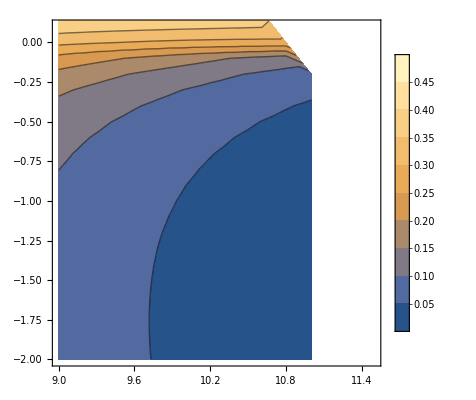

```mathematica
ListContourPlot[pts,PlotLegends->Automatic,PlotRange->{{9,11.5},{-2,.1}}]
```

```mathematica
t=5;
logRCA = -1;
norm = NIntegrate[Exp[-Abs[g-0.03]/(c1 +c2 Exp[-t/x0])]/(c1 +c2 Exp[-t/x0]),{g,-Infinity,Infinity}];
NIntegrate[Exp[-Abs[g-0.03]/(c1 +c2 Exp[-t/x0])]/(c1 +c2 Exp[-t/x0]),{g,-logRCA,Infinity}]/norm
```

0.0600202

```mathematica
(*pts = Flatten[Table[Table[t = logRCA+Xc+Xp-Xw;{Xc+Xp-Xw,logRCA,NIntegrate[Exp[-Abs[g-0.00]/Exp[bfit[Xc]]]/(2Exp[bfit[Xc]]),{g,-logRCA,Infinity}]},{Xc,8,12.5,.2}],{logRCA,-2.5,1,0.1}],1];*)
```

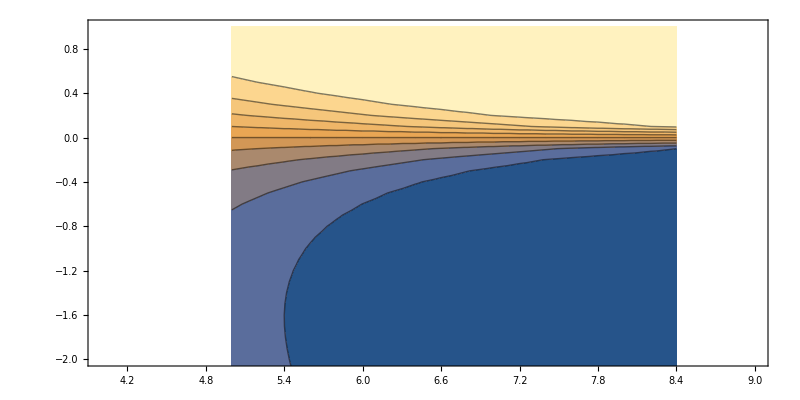

```mathematica
ListContourPlot[pts,PlotLegends->Automatic,PlotRange->{{4,9},{-2,1}},AspectRatio->1/2,ImageSize->800]
```

```mathematica
xy = Flatten[Table[Table[{Xc, logRCA},{Xc,7,10,.2}],{logRCA,-1,.5,0.1}],1];
```

### Numerical integration of p(g)

```mathematica
SetDirectory[NotebookDirectory[]];
numRCAHiRes = Import["numericalRCA_HiRes.csv"]//Rest;
numRCALoRes = Import["numericalRCA_LowRes.csv"]//Rest;
```

```mathematica
pts = Flatten[Table[Table[xcp= logRCA+T;{T,logRCA,NIntegrate[Exp[-Abs[g-0.00]/10^(bfit[xcp])]/(2 10^(bfit[xcp])),{g,-logRCA,Infinity}]},{T,4,9.5,.2}],{logRCA,-1,1,0.1}],1]//Quiet;
```

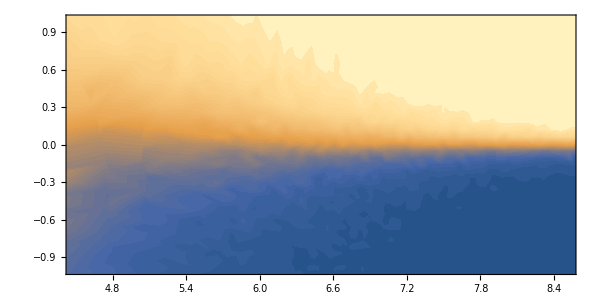

```mathematica
ListContourPlot[numRCAHiRes,PlotLegends->Automatic,PlotRange->{{4.5,8.5},{-1,1}},AspectRatio->1/2,ImageSize->600,ContourStyle->None,Contours->50]
(*ListContourPlot[pts,PlotRange->{{4.5,8.5},{-1,1}},AspectRatio->1/2,ImageSize->600,ContourStyle->None,Contours->50]*)
```

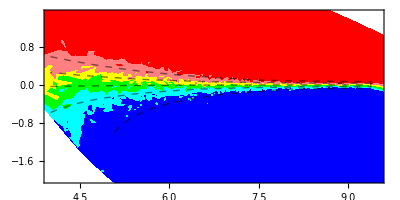

```mathematica
Show[ListContourPlot[numRCA,PlotLegends->Automatic,PlotRange->{{4,9.5},{-2,1.5}},AspectRatio->1/2,ImageSize->400,ContourStyle->None,ContourShading->{Blue,Cyan,Green,Yellow,Pink,Red},Contours->5],ListContourPlot[pts,PlotRange->{{4,8.5},{-2,1.5}},AspectRatio->1/2,ImageSize->400,ContourStyle->Directive[Thick, Dashed],ContourShading->None,Contours->5]]
```

### Map in High Resolution

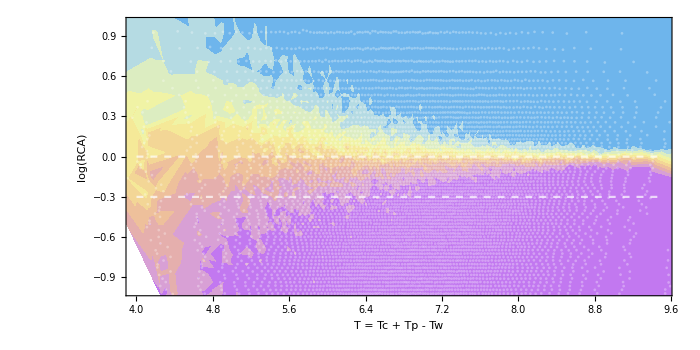

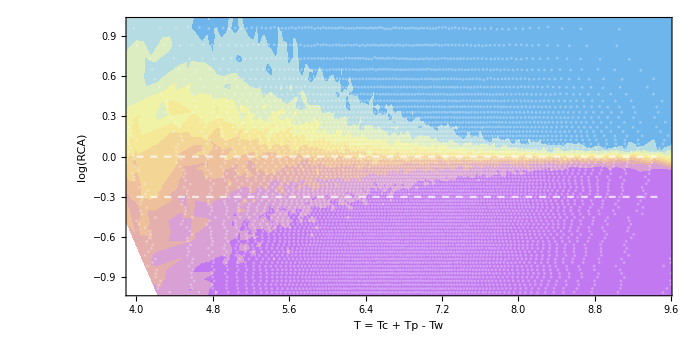

numericalRCA.png

```mathematica
Show[ListContourPlot[numRCAHiRes,PlotLegends->Automatic,PlotRange->{{4,9.5},{-1,1}},AspectRatio->1/2,ContourStyle->None,ColorFunction->"Pastel",Contours->9],ListPlot[numRCAHiRes[[All,1;;2]],PlotStyle->Opacity[.3,White]],Plot[{Log10[1],Log10[.5]},{x,4,9.5},PlotStyle->Directive[Opacity[.7,White],Dashed]],ImageSize->700,Frame->True,FrameLabel->{"T = Tc + Tp - Tw ", "log(RCA)","Probability of achieving RCA > 1 in following year"},LabelStyle->16]
Export["numericalRCA.png",%]
```

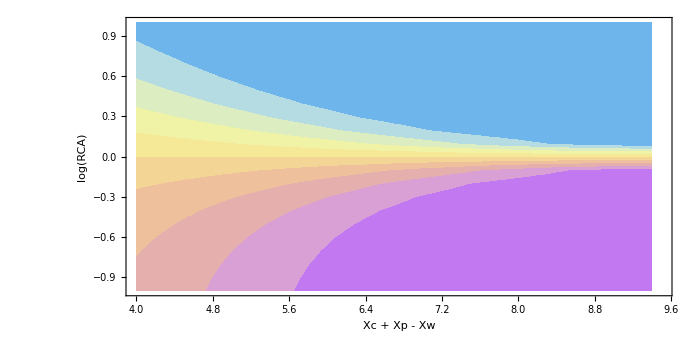

```mathematica
ListContourPlot[pts,PlotLegends->Automatic,PlotRange->{{4,9.5},{-1,1}},AspectRatio->1/2,ImageSize->700,ContourStyle->None,ColorFunction->"Pastel",Contours->9,FrameLabel->{"Xc + Xp - Xw ", "log(RCA)","Probability of achieving \n RCA > 1 in following year"},LabelStyle->16]
```

### Comparison of contours

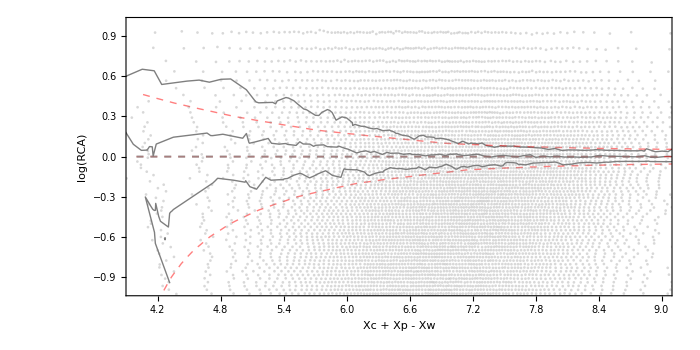

```mathematica
Show[ListContourPlot[numRCALoRes,PlotLegends->Automatic,PlotRange->{{4,9},{-1,1}},AspectRatio->1/2,ContourShading->None,Contours->{.25,.5,.75},ContourStyle->Thick],
ListContourPlot[pts,PlotLegends->Automatic,PlotRange->{{4,8.5},{-.3,.3}},AspectRatio->1/2,ContourShading->None,Contours->{.25,.5,.75},ContourStyle->Directive[Dashed,Thick,Red]],ListPlot[numRCA[[All,1;;2]],PlotStyle->Opacity[.3,Gray]],Plot[{Log10[1]},{x,4,9},PlotStyle->Directive[Opacity[.7,Gray],Dashed]],ImageSize->700,Frame->True,FrameLabel->{"Xc + Xp - Xw ", "log(RCA)","Probability of achieving RCA > 1 in following year"},LabelStyle->16]
```

## RCA Matrix

```mathematica
SetDirectory[NotebookDirectory[]];
spData = Import["SpArray.csv"]//Rest;
spData[[All,2;;3]] = spData[[All,2;;3]]//IntegerPart;
```

```mathematica
rowticks = SortBy[spData[[All,{3,6}]]//DeleteDuplicates,First];
colticks = SortBy[spData[[All,{2,5}]]//DeleteDuplicates,First];
colticks[[All,2]]  = StringTake[#,UpTo[10]]&/@colticks[[All,2]] ;
myTickList[shift_?NumericQ,phi_?NumericQ]:=Table[{i,Rotate[Pane[Style[ToString[colticks[[i,2]]]],FrameMargins->{{0,0},{0,0}}],phi]},{i,Length[colticks]}]
```

```mathematica
Table[MatrixPlot[Transpose[SparseArray[#[[2;;3]]-> (2Round[#[[4]],def]-1)&/@spData,Automatic,1]],ImageSize->1000,ColorFunction->"GrayTones",FrameTicks->{None,None,rowticks,myTickList[1, Pi/2]},ColorFunctionScaling->False,LabelStyle->15],{def,{1,0.5,0.33,0.2,0.1,0.01}}]
Export["McpSample.gif",%,"DisplayDurations"->.5]
```

$Aborted

```mathematica
spData = Import["SpArray.csv"]//Rest;
spData[[All,2;;3]] = spData[[All,2;;3]]//IntegerPart;
```

```mathematica
matrixPermut[M_,list1_,list2_]:= M[[Ordering[list1],Ordering[list2]]]
```

```mathematica
Mcp = Normal[Transpose[SparseArray[#[[2;;3]]-> #[[4]]&/@spData,Automatic,0]]];
p1=Count[#,1]&/@(Mcp);
p2=Count[#,1]&/@(Mcpᵀ);
t=matrixPermut[Mcp,p1,p2];
```

```mathematica
cat2[x_]:=Piecewise[{{White,0≤x≤0.5},{Black,0.5<x≤1}}]
cat3[x_]:=Piecewise[{{White,0≤x≤0.2},{Yellow,0.2<x≤0.8},{Black,0.75<x≤1}}]
```

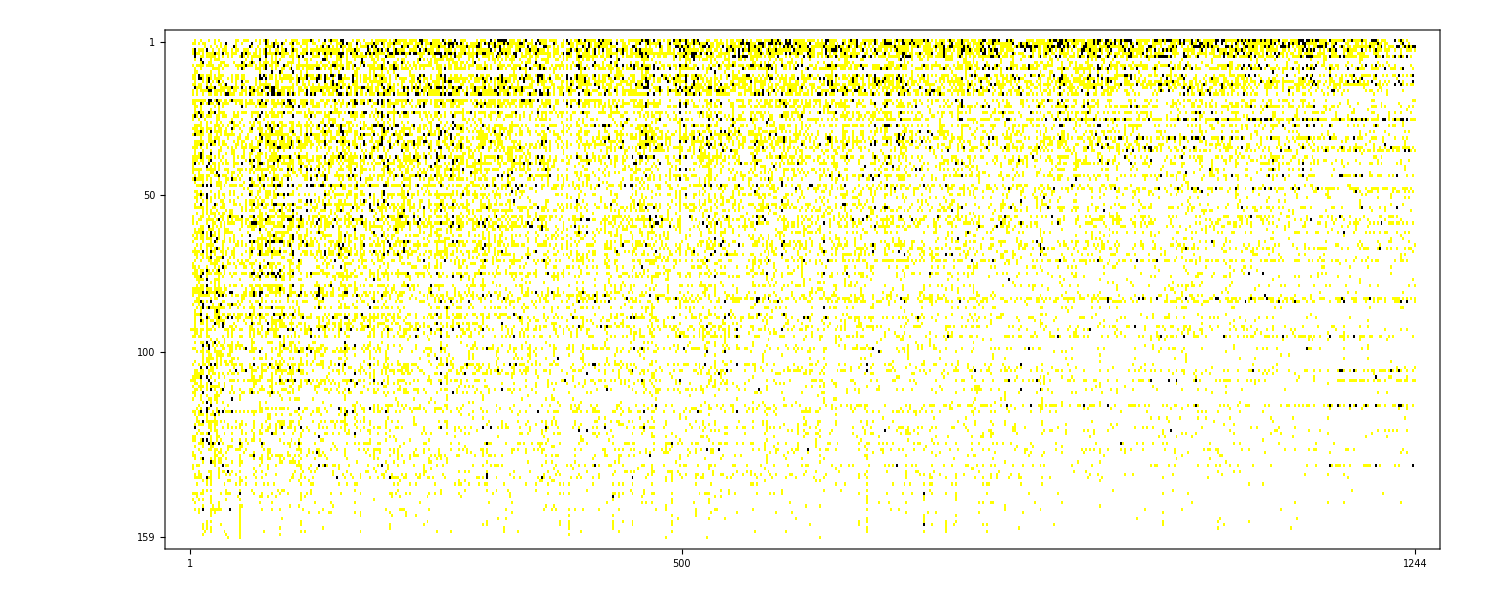
{-Graphics-,-Graphics-}

fullMatrix.gif

```mathematica
Table[MatrixPlot[Transpose[t],ImageSize->1500,ColorFunction->i,ColorFunctionScaling->False,LabelStyle->15],{i,{cat2,cat3}}]
Export["fullMatrix.gif",%,"DisplayDurations"->.5]
```

```mathematica
Histogram[t//Flatten, {{0,.2,.8,1}}]
```